```mathematica
ImportCsv[name_] := Import["~/workspace/PBLL/LieDetector/Analysis/" <> name <> ".csv","Dataset","HeaderLines"->1]
```

```mathematica
IndividualMeansFromCenter[name_, selectColumn_:null,selectValue_:null] :=
Block[{columns, dataset, allValues, center, grouped, groupedColumns, groupedValues, allDistances, allMeans},
columns = {"Combine Gaze X","Combine Gaze Y"};
dataset=If[selectColumn ≠ null,Select[ImportCsv[name], #[selectColumn] == selectValue&], ImportCsv[name]];
allValues=Values[dataset[All,columns]];
center={Mean[allValues[All,1]],Mean[allValues[All,2]]};

grouped=dataset[GroupBy["Index"]];
groupedColumns = Table[grouped[[x]][All, columns], {x, 1, Length[grouped], 1}];
groupedValues = (Normal[Values[#]])& /@ groupedColumns;
allDistances=((ArcLength[Line[{#,center}]])& /@ #)&/@groupedValues;
allMeans = (Mean[#])& /@ allDistances;
Drop[allMeans, 1]
]
```

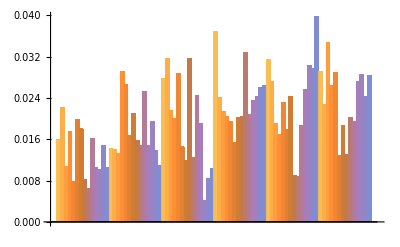

```mathematica
BarChart[{IndividualMeansFromCenter["truth"], IndividualMeansFromCenter["truth2"], IndividualMeansFromCenter["truth3"], IndividualMeansFromCenter["lies"], IndividualMeansFromCenter["lies2"], IndividualMeansFromCenter["lies3"]}]
```

```mathematica
baseline = Mean[IndividualMeansFromCenter["truth3"]]
```

0.0190438

```mathematica
Mean[Join[IndividualMeansFromCenter["lies"], IndividualMeansFromCenter["lies2"], IndividualMeansFromCenter["lies3"]]]
```

0.0235469

```mathematica
Mean[IndividualMeansFromCenter["mixed"]]
```

0.0127355

```mathematica
Pupils[name_] :=
Block[{columns, dataset, allValues, center, grouped, groupedColumns, groupedValues, allMeans},
columns = {"Left Pupil Diameter", "Right Pupil Diameter"};
dataset=Select[ImportCsv[name], (#["Color"] == "Red")&];

grouped=dataset[GroupBy["Index"]];
groupedColumns = Table[grouped[[x]][All, columns], {x, 1, Length[grouped], 1}];
groupedValues = (Normal[Values[#]])& /@ groupedColumns;
allMeans = (Mean[Mean[{#[[1]], #[[2]]}]])& /@ groupedValues;
allMeans
]
```

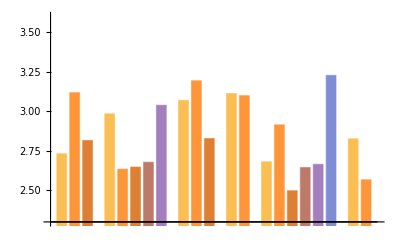

```mathematica
BarChart[{Pupils["truth"], Pupils["truth2"], Pupils["truth3"], Pupils["lies"], Pupils["lies2"], Pupils["lies3"]}, PlotRange->{{2.3,3.6}}]
```

```mathematica
Mean[Join[Pupils["truth"], Pupils["truth2"], Pupils["truth3"]]]
```

2.88514

```mathematica
Mean[Join[Pupils["lies"], Pupils["lies2"], Pupils["lies3"]]]
```

```mathematica
2.8233147
```

```mathematica
colors = (If[# == "FALSE",Red,Blue])& /@Normal[Values[((#[[1]])&/@ImportCsv["mixed"][GroupBy["Index"]])[All, "Truth"]]]
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}

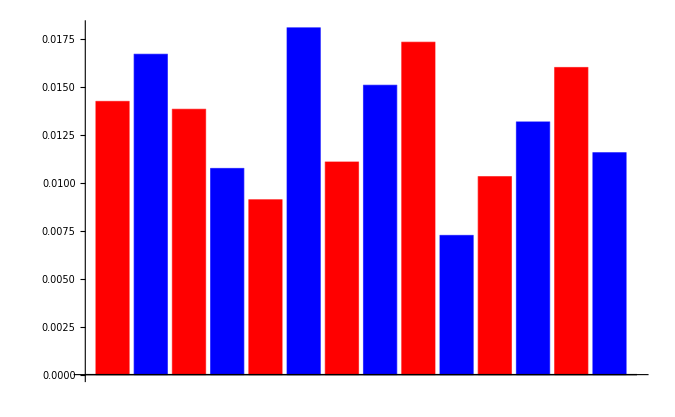

```mathematica
BarChart[IndividualMeansFromCenter["mixed"], ChartStyle-> colors]
```

```mathematica
TimeToAnswer[name_] := 
Block[{dataset, grouped, times},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["Index"]];
times = Table[grouped[[x]][All, "Total Time"], {x, 1, Length[grouped], 1}];
(Last[#] - First[#])& /@ times
]
```

```mathematica
baselineTime = Mean[TimeToAnswer["truth3"]]
```

1.38023

```mathematica
baselineEye = Mean[IndividualMeansFromCenter["truth3"]]
```

0.0190438

```mathematica
Mean[(Abs[baselineEye - #])& /@ IndividualMeansFromCenter["mixed"]]
```

0.00630832